```mathematica
Lx=10;Ly=3;Lz=25;M=8.8*10^5;Subscript[μ, 0]=4π*10^-7;
B`single`magnet`x[x_,y_,z_,Mx_,My_,Mz_]:=Subscript[μ, 0]*M/(4π)*Sum[(-1)^(k+l+m)*Log[(z-Mz)+(-1)^m(Lz/2)+√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2)],{k,1,2},{l,1,2},{m,1,2}];
B`single`magnet`y0[x_,y_,z_,Mx_,My_,Mz_]:=Subscript[μ, 0]*-M/(4π)*Sum[(-1)^(k+l+m)*(((y-My)+(-1)^l(Ly/2))((x-Mx)+(-1)^k(Lx/2)))/(Abs[(y-My)+(-1)^l(Ly/2)]*Abs[(x-Mx)+(-1)^k(Lx/2)])*ArcTan[(Abs[(x-Mx)+(-1)^k(Lx/2)]*((z-Mz)+(-1)^m(Lz/2)))/(Abs[(y-My)+(-1)^l(Ly/2)]*√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2))],{k,1,2},{l,1,2},{m,1,2}];
B`single`magnet`y[x_,y_,z_,Mx_,My_,Mz_]:=If[Abs[y]≤Ly/2&&Abs[x]≤Lx/2&&Abs[z]≤Lz/2,-B`single`magnet`y0[x,y,z,Mx,My,Mz],B`single`magnet`y0[x,y,z,Mx,My,Mz]];
B`single`magnet`z[x_,y_,z_,Mx_,My_,Mz_]:=Subscript[μ, 0]*M/(4π)*Sum[(-1)^(k+l+m)*Log[(x-Mx)+(-1)^k(Lx/2)+√(((x-Mx)+(-1)^k(Lx/2))^2+((y-My)+(-1)^l(Ly/2))^2+((z-Mz)+(-1)^m(Lz/2))^2)],{k,1,2},{l,1,2},{m,1,2}];

BSX[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[B`single`magnet`x[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BSY[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[B`single`magnet`y[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BSZ[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sum[B`single`magnet`z[x,y,z,Xstack,Ystack+i*Ly,Zstack],{i,-4,4}];
BS[x_,y_,z_,Xstack_,Ystack_,Zstack_]:=Sqrt[BSX[x,y,z,Xstack,Ystack,Zstack]^2+BSY[x,y,z,Xstack,Ystack,Zstack]^2+BSZ[x,y,z,Xstack,Ystack,Zstack]^2];
```

```mathematica
stackposition1={37,0,49};
stackposition2={37,0,-49};
stackposition3={-37,0,49};
stackposition4={-37,0,-49};
```

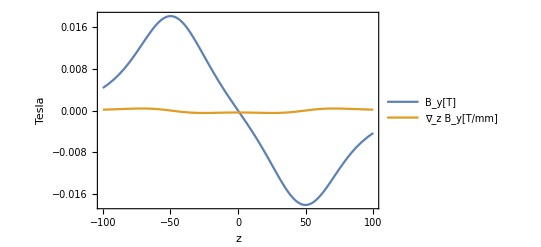

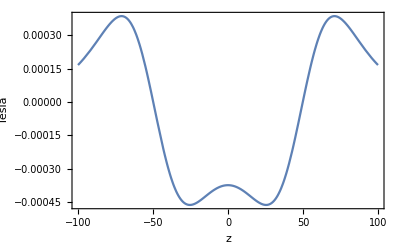

```mathematica
BYcentral[z_]:=-BSY[0,0,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,0,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,0,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,0,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
len=2000;δz=200/len;z0=-100;
dataB=Table[{z0+i*δz,BYcentral[z0+i*δz]},{i,0,len}];
(*data∇B=Table[{z0+i*δz,(BYcentral[z0+(i+1)*δz]-BYcentral[z0+i*δz])/δz},{i,0,len}];*)
BYcc=Interpolation@dataB;
(*gradient=Interpolation@data∇B;*)
Plot[{BYcc[z],BYcc'[z]},{z,-100,100},PlotLegends->{"B_y[T]","∇_z B_y[T/mm]"},Frame->True,FrameLabel->{"z","Tesla"}]
Plot[BYcc'[z],{z,-100,100},Frame->True,FrameLabel->{"z","Tesla"}]
```

```mathematica
StreamDensityPlot[{-BSY[0,y,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,y,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,y,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,y,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]],-BSZ[0,y,z,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]+-BSZ[0,y,z,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSZ[0,y,z,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSZ[0,y,z,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]]},{y,-100,100},{z,-100,100}]
```

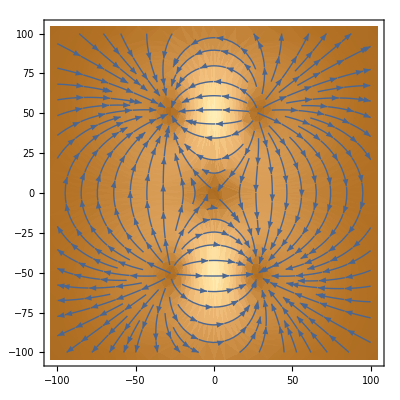

```mathematica
BYcentral[y_]:=-BSY[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSY[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSY[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSY[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
BXcentral[y_]:=-BSX[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSX[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSX[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSX[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
BZcentral[y_]:=-BSZ[0,y,0,stackposition2[[1]],stackposition2[[2]],stackposition2[[3]]]-BSZ[0,y,0,stackposition4[[1]],stackposition4[[2]],stackposition4[[3]]]+BSZ[0,y,0,stackposition1[[1]],stackposition1[[2]],stackposition1[[3]]]+BSZ[0,y,0,stackposition3[[1]],stackposition3[[2]],stackposition3[[3]]];
Bmagnitude[y_]:=Sqrt[BXcentral[y]^2+BYcentral[y]^2+BZcentral[y]^2];
leny=2000;δy=90/leny;y0=-100;
datamagnitude=Table[{y0+i*δy,Bmagnitude[y0+i*δy]},{i,0,leny}];
Max[datamagnitude[[All,2]]]
BMa=Interpolation@datamagnitude;
Plot[BMa[y],{y,-100,-10}]
```

0.00681302

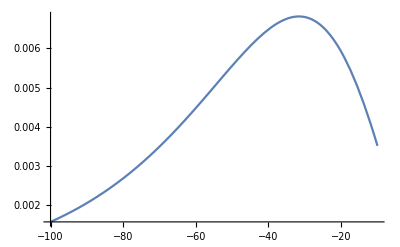

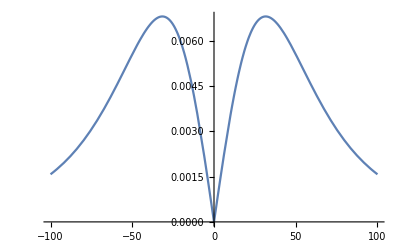

```mathematica
Plot[Bmagnitude[y],{y,-100,100}]
```

```mathematica
μ=4π*10^-7;A=400;L`solenoid=0.02;r1=3.75*10^-2;r2=6.1*10^-2;r3=8.5*10^-2;distance=5.75*10^-2;n=11;R1=(r1+r2)/2;R2=(r2+r3)/2;
sincoil[r_,y_,poc_]:=(μ*A)/2*r^2/((r^2+(y-poc)^2)^(3/2));
(*solenoid[r_,y_]:=n*sincoil[r,y,0];*)
solenoid[r_,y_]:=Sum[sincoil[r,y,i*(L`solenoid)/n],{i,-5,5,1}];
B`inner[y_]:=solenoid[R1,distance/2+y]+solenoid[R1,y-distance/2];
B`outer[y_]:=solenoid[R2,distance/2+y]+solenoid[R2,y-distance/2];
B`total[y_]:=B`inner[y]+B`outer[y];
```

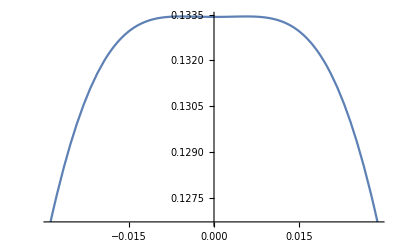

```mathematica
Plot[B`total[y],{y,-distance/2,distance/2}]
```

```mathematica
B`inner[0]/A
```

0.000181459

```mathematica
B`outer[0]/A
```

0.000152116

```mathematica
μ=4π*10^-7;A=400;L`solenoid=0.02;r1=3.75*10^-2;r2=6.1*10^-2;r3=8.5*10^-2;distance=5.75*10^-2;n=11;R1=(r1+r2)/2;R2=(r2+r3)/2;
single`z[r_,x_,y_,z_,poc_]:=(μ*A*r)/(4π)*NIntegrate[(Cos[θ]*(y-poc))/(((z-r*Cos[θ])^2+(x-r*Sin[θ])^2+(y-poc)^2)^(3/2)),{θ,0,2π}];
single`x[r_,x_,y_,z_,poc_]:=(μ*A*r)/(4π)*NIntegrate[(Sin[θ]*(y-poc))/(((z-r*Cos[θ])^2+(x-r*Sin[θ])^2+(y-poc)^2)^(3/2)),{θ,0,2π}];
single`y[r_,x_,y_,z_,poc_]:=(μ*A*r)/(4π)*NIntegrate[(r-z*Cos[θ]-x*Sin[θ])/(((z-r*Cos[θ])^2+(x-r*Sin[θ])^2+(y-poc)^2)^(3/2)),{θ,0,2π}];
solenoid`x[r_,x_,y_,z_]:=Sum[single`x[r,x,y,z,i*(L`solenoid)/n],{i,-5,5,1}];
solenoid`y[r_,x_,y_,z_]:=Sum[single`y[r,x,y,z,i*(L`solenoid)/n],{i,-5,5,1}];
solenoid`z[r_,x_,y_,z_]:=Sum[single`z[r,x,y,z,i*(L`solenoid)/n],{i,-5,5,1}];
B`helmholtz`x[r_,x_,y_,z_]:=solenoid`x[r,x,distance/2+y,z]+solenoid`x[r,x,y-distance/2,z];
B`helmholtz`y[r_,x_,y_,z_]:=solenoid`y[r,x,distance/2+y,z]+solenoid`y[r,x,y-distance/2,z];
B`helmholtz`z[r_,x_,y_,z_]:=solenoid`z[r,x,distance/2+y,z]+solenoid`z[r,x,y-distance/2,z];
```

```mathematica
Plot[B`helmholtz`y[R1,0,y,0]+B`helmholtz`y[R2,0,y,0],{y,-distance/2,distance/2}]
```

-Graphics-

```mathematica
B[R1,0,0,0]
```

0.0725835

```mathematica
Plot[B`single`magnet`y[0,0,0,0,My,0]+B`inner[0]+B`outer[0],{My,-distance,distance}]
```

```mathematica
Clear["Global`*"]
```